# Cuaderno de Prácticas

## Análisis y métodos numéricos

## Grado en Ingeniería Informática

## CURSO 2024/25

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : 2
Grupo de prácticas :

## Tema 1. Números reales

### Problemas de ecuaciones con valor absoluto

## 1.- Resolver ||x-1|-1|=1 Enero 18

Solución:
Si el valor absoluto de una expresión vale a, entonces la expresión puede tomar dos valores, a ó -a. Sabiendo esto obtenemos:
	 ||x-1|-1|=1 ⟹ |x-1|-1=1 ó  |x-1|-1=-1 
En el primer caso, 	 |x-1|-1=1 ⟹ |x-1|= 2 ⟹ x-1= 2 ó -2 ⟹ x =3 ó -1
En el segundo caso,  |x-1|-1=-1 ⟹ |x-1|= 0 ⟹ x-1= 0 ⟹ x= 1

Hay 3 soluciones: -1, 1 y 3.
Con el Mathematica,

```mathematica
Reduce[Abs[Abs[x-1]-1]==1,x,Reals]
```

x==-1||x==1||x==3

### Problemas de inecuaciones con valor absoluto

## 1.- Resolver ||x-1|-1|<1 Octubre 2021

Solución:
Si el valor absoluto de una expresión vale menos de un número positivo a, entonces la expresión está entre -a y a. Sabiendo esto obtenemos:
	 ||x-1|-1|<1 ⟹ -1<|x-1|-1<1 ⟹(sumando 1 en cada término) ⟹ 0<|x-1|< 2 
Es decir, deben cumplirse las dos condiciones:
	0<|x-1|
	|x-1|< 2 
La primera desigualdad significa que x es distinto de 1, x ≠1,  y la segunda que  -2<x-1<2 .

En resumen,  x ≠1  y -1< x <3.

Por tanto, las soluciones son los números de los intervalos (-1,1) y (1,3).

Con el Mathematica

```mathematica
Reduce[Abs[Abs[x-1]-1]<1,x,Reals]
```

-1<x<1||1<x<3

### Problemas de inducción

## 1.- Demostrar, usando inducción, que 1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3 para n = 1, 2, 3, 4, ... Julio-Octubre 18

Solución:
Para realizar la demostración por inducción, comenzamos estudiando el primer caso, n=1. 
El primer término, que empieza con 1*2, debe terminar cuando n=1 con 1*(1+1), por tanto se reduce a un sumando. La igualdad que habría que comprobar es:
1*2  = (1(1+1)(1+2))/3. Es inmediato comprobar que ambas expresiones valen 2.
En la segunda parte del método de inducción, se supone que la propiedad es cierta para un valor n y se trata de comprobar que también lo es para (n+1).

Es decir, si la igualdad es cierta para n, 1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3, se trataría de demostrar que también lo será para (n+1).

El primer termino de la expresión para (n+1) es:
1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+1+1) =1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) 

El segundo término de la expresión para n+1 es
 ((n+1)((n+1)+1)((n+1)+2))/3 = ((n+1)(n+2)(n+3))/3
Tenemos que demostrar que si es cierto para n, también lo es para n+1, es decir que si  1*2 + 2*3 + 3*4 + ...+ n(n+1) = (n(n+1)(n+2))/3 también será cierto que
	1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) =((n+1)(n+2)(n+3))/3
Observamos que los primeros sumandos de la primera expresión son los de la expresión para n, por tanto,
 1*2 + 2*3 + 3*4 + ...+ n(n+1)+ (n+1)(n+2) =(n(n+1)(n+2))/3 + (n+1)(n+2) = (n+1)(n+2)(n/3+1) =(n+1)(n+2)((n+3)/3) = ((n+1)(n+2)(n+3))/3
 y concluimos que de ser cierta la igualdad para n, también lo es para (n+1).

### Otros problemas

## 1.- Razonar cuál de los siguientes números es racional y expresarlo como cociente de dos números enteros: 0,010101010101... = ∑_(n=1)^∞ 1/10^(2n) , 0,1001000010000001.... = ∑_(n=1)^∞ 1/(10^(n^2)) . Julio 2023

Comentarios:
Los números racionales son los cocientes de números enteros, a/b, con b>0. Al realizar la división de a entre b, puede obtenerse un número entero, en otro caso, para obtener una forma numérica decimal, “sacamos decimales” y tiene que llegar un momento en que los restos posibles (que serán números entre 0 y b-1) se tienen que repetir de forma indefinida y se origina un periodo. De igual forma, si un número tiene un desarrollo decimal, donde a partir de un momento, una sucesión de cifras se repite sucesivamente y de forma indefinida, podemos expresar el número como cociente de dos enteros. 
Además de los racionales, hay más números, algunos utilizados con mucha frecuencia como la raíz de dos, el número π, el logaritmo de 2, etc. Estos números forman parte de los irracionales, números reales que no son racionales. Estos números no tienen un desarrollo decimal periódico.

Solución:
Observamos que el primer número es periódico. El par de cifras 01 se repite continuamente. Se trata de un número racional. Para ponerlo como fracción escribimos
				x = 0,01010101...   
			100 x = 1,01010101...
Restando de la segunda expresión la primera:  99 x = 1. Por tanto, x=1/99.

El segundo número tiene un desarrollo decimal que no es periódico. Hay dos ceros entre los primeros dos unos, luego hay cuatro ceros, después seis ceros, etc. No es un número racional.
 
Con el Mathematica sería:

```mathematica
Sum[1/10^(2n),{n,1,Infinity}]
```

1/99

```mathematica
Sum[1/10^(n^2),{n,1,Infinity}]
```

1/2 (-1+EllipticTheta[3,0,1/10])

## 5.- Expresar el número 12’345454545... como cociente de dos números enteros. Julio 22

Llamando               x=12’345454545... 
Tenemos que 10 x = 123’45454545... 
También       1000x = 12345’454545...
Restando, 1000x - 10x = 12345-123. Por tanto, 990 x = 12222, x=12222/990.  Si queremos simplificar, que no es necesario, dividimos numerador y denominador por 2 y por 9. 12222/990 = 1358/110 = 679/55.

Otra forma sería escribir el número como una suma con una serie geométrica (y aplicar la fórmula para la suma en este caso).

12’3454545... = 12 +  3/10+ ∑_(n=1)^∞ 45/(10*100^n) = 120/10 +  3/10+45/10 ∑_(n=1)^∞ 1/100^n = 123/10 +45/10 (1/100)/(1-1/100) = 123/10 +45/10 1/(100-1) = 123/10 +45/10 1/99 = 123/10 +45/990 = 123/10 +5/110 = 123/10 +1/22 = (123*22+10)/220 =  2716/220= 2716/220 = 679/55

## 1.- Obtener los valores de x para los que x^2 < |x|. Expresar el conjunto por medio de intervalos, decir si es abierto o cerrado, si está acotado superior o inferiormente, si tiene máximo o mínimo, supremo o ínfimo. Enero 2019

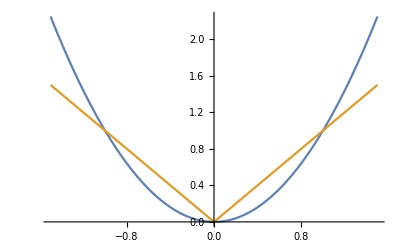
Solución: 	
El valor absoluto de x puede ser x ó -x, según sea x mayor o menor que cero. Distinguimos los dos casos:
	Cuando x es mayor que cero, la desigualdad queda como:  x^2 < |x|=x . Estudiaremos la desigualdad:   x^2 < x . Restando x,   x^2-x<0 ⟹ x(x-1)<0. Como x>0 ⟹ x-1 debe ser menor que 0 ⟹ x<1
	
	Cuando x es menor que cero,  la desigualdad queda como:  x^2 < |x|=-x . Estudiaremos la desigualdad:   x^2 < -x . Sumando x,   x^2+x<0 ⟹ x(x+1)<0. Como x<0 ⟹ x+1 debe ser mayor que 0 ⟹ x>-1
	
En el caso x=0, no se cumple la desigualdad.

Por tanto, cuando x es mayor que cero, debe ser menor que 1 y cuando x es menor que cero, debe ser mayor que -1. Luego el conjunto es (-1,0) ∪ (0,1). 
Se trata de un conjunto abierto, acotado superior e inferiormente, el supremo es 1, el ínfimo es -1, no tiene máximo, ni mínimo.

Si dibujamos las gráficas de las dos funciones:
			-Graphics-
Vemos que el valor absoluto está por encima de la gráfica de x^2 cuando x está en (-1,0) y en (0,1).
 
Con el Mathematica,

```mathematica
Reduce[x^2<Abs[x],x,Reals]
```

-1<x<0||0<x<1

## Tema 2. Números complejos

### Problemas de cálculos

## 2.- Calcular ((1-3ⅈ)/(1+2ⅈ))^20. Dar la parte real e imaginaria de la solución. Enero 23

Solución:
Comenzamos calculando la fracción. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1-3ⅈ)/(1+2ⅈ) = ((1-3ⅈ)(1-2ⅈ))/((1+2ⅈ)(1-2ⅈ)) = (1-5ⅈ+6 ⅈ^2)/(1+4)=(-5-5ⅈ)/5=-1-ⅈ   ⟹  ((1-3ⅈ)/(1+2ⅈ))^4 = (-1-ⅈ)^4 =  (-1-ⅈ)^2 (-1-ⅈ)^2 = (1+ⅈ^2+2ⅈ)^2 = (2ⅈ)^2 = -4

## 2.- Razonar en qué cuadrante está el número complejo ((1+3ⅈ)/(1-2ⅈ))^23. Julio 23

Solución:
Comenzamos calculando el cociente que aparece. Para ello multiplicamos y dividimos por el conjugado del denominador.
(1+3ⅈ)/(1-2ⅈ) = ((1+3ⅈ)(1+2ⅈ))/((1-2ⅈ)(1+2ⅈ)) = (1+5ⅈ+6 ⅈ^2)/(1+4)=(-5+5ⅈ)/5= - 1 + ⅈ   ⟹  ((1+3ⅈ)/(1-2ⅈ))^23 = (-1+ⅈ)^23 

El argumento de - 1 + ⅈ es (3π)/4, pues está en la bisectriz del segundo cuadrante (parte real negativa y parte imaginaria positiva). Al elevar el número a 23, el argumento se multiplicará por 23. Por tanto, será (23*3π)/4= (69π)/4= ((64+5)π)/4 = 16 π+ (5π)/4 = 8*(2 π) + (5π)/4. Por tanto, el argumento es 8 vueltas completas más (5π)/4 y estará en el tercer cuadrante.

Otra posibilidad es calcular  (-1+ⅈ)^23
(-1+ⅈ)^2= (-1+ⅈ) (-1+ⅈ) = -2ⅈ
(-1+ⅈ)^4=(-1+ⅈ)^2(-1+ⅈ)^2=  (-2ⅈ)(-2ⅈ) = -4
(-1+ⅈ)^8=(-1+ⅈ)^4(-1+ⅈ)^4=  (-4)(-4) = 16
(-1+ⅈ)^16=(-1+ⅈ)^8(-1+ⅈ)^8 =  16*16 = 256
(-1+ⅈ)^23=(-1+ⅈ)^16(-1+ⅈ)^4(-1+ⅈ)^2(-1+ⅈ) = 256*(-4)*(-2ⅈ)*(-1+ⅈ) = -1024 (2+2ⅈ) = -2048-2048 ⅈ
Así vemos que está en el tercer cuadrante al tener tanto la parte real como imaginaria negativas.
 
Con el Mathematica,

```mathematica
((1+3ⅈ)/(1-2ⅈ))^23
```

-2048-2048 ⅈ

Vemos que tanto la parte real como la imaginaria son negativas, por tanto está en el tercer cuadrante.

## 2.- Calcular el módulo y el argumento de 1+ ⅈ ⅇ^(π/2 ⅈ)+ⅈ^2 ⅇ^(π/2 ⅈ^2)+ⅈ^3 ⅇ^(π/2 ⅈ^3). Enero 23

Solución:
En primer lugar, y teniendo en cuenta que ⅈ^2 = -1, ⅈ^3 = - ⅈ,
1+ ⅈ ⅇ^(π/2 ⅈ)+ⅈ^2 ⅇ^(π/2 ⅈ^2)+ⅈ^3 ⅇ^(π/2 ⅈ^3)=1+ ⅈ ⅇ^(π/2 ⅈ)- ⅇ^(-π/2)-ⅈ ⅇ^(-π/2ⅈ) =
(Teniendo en cuenta que la exponencial de un número complejo es  ⅇ^(a+ⅈb)=ⅇ^a(cos b + ⅈ sen b))
	= 1+ ⅈ (cos(π/2)+ⅈ sen(π/2))- ⅇ^(-π/2)-ⅈ (cos(-π/2)+ⅈ sen(-π/2)) = 1+ ⅈ *ⅈ - ⅇ^(-π/2)-ⅈ (-ⅈ ) = 1-1 - ⅇ^(-π/2)-1 = - ⅇ^(-π/2)-1 
La expresión resulta ser un número real negativo. Por tanto, el argumento será π radianes y el módulo su valor absoluto   ⅇ^(-π/2)+1.
Con el Mathematica,

```mathematica
1+ⅈ ⅇ^(π/2 ⅈ)+ⅈ^2 ⅇ^(π/2 ⅈ^2)+ⅈ^3 ⅇ^(π/2 ⅈ^3)
```

-1-ⅇ^(-π/2)

```mathematica
Abs[1+ⅈ ⅇ^(π/2 ⅈ)+ⅈ^2 ⅇ^(π/2 ⅈ^2)+ⅈ^3 ⅇ^(π/2 ⅈ^3)]
```

1+ⅇ^(-π/2)

```mathematica
Arg[1+ⅈ ⅇ^(π/2 ⅈ)+ⅈ^2 ⅇ^(π/2 ⅈ^2)+ⅈ^3 ⅇ^(π/2 ⅈ^3)]
```

π

### Problemas de resolución de ecuaciones

## 2.- Resolver la ecuación z^3 = z/(1+ⅈ) y calcular los módulos y argumentos de sus soluciones. Octubre 22, Octubre 21

Solución:
Operamos para despejar.
z^3 = z/(1+ⅈ) ⟹ z^3 - z/(1+ⅈ)=0 ⟹ z(z^2 - 1/(1+ⅈ))=0  ⟹ z = 0 ó (z^2 - 1/(1+ⅈ))=0 ⟹ z = 0 ó z^2 = 1/(1+ⅈ)
Calculamos 1/(1+ⅈ) = (1-ⅈ)/((1+ⅈ)(1-ⅈ))= (1-ⅈ)/2 = 1/2-ⅈ/2. Expresado en forma polar (módulo y argumento) será (√(1/2))_(-π/4) (está en la bisectriz del cuarto cuadrante)
Calculamos las raíces cuadradas de  (√(1/2))_(-π/4). 
Recordemos que la raíz n-ésima de un número complejo z, con módulo r y argumento θ son n valores en la forma:
		z^(1/n)= r_θ^(1/n)={ (r^(1/n))_(θ/n),  (r^(1/n))_(θ/n+(2π)/n),  (r^(1/n))_(θ/n+2(2π)/n), ..., (r^(1/n))_(θ/n+(n-1)(2π)/n)}

Por tanto, realizamos la raíz cuadrada del módulo y dividimos por dos el argumento (también el argumento más 2π)
		((1/2)^(1/4))_(-π/8),	((1/2)^(1/4))_(-π/8+π)=	((1/2)^(1/4))_(7π/8)
Las tres soluciones de la ecuación son: z=0, z= ((1/2)^(1/4))_(-π/8) y z=((1/2)^(1/4))_(7π/8). Los módulos son 0, (1/2)^(1/4) y (1/2)^(1/4), respectivamente. Los argumentos de las soluciones distintas del cero son -π/8 y 7π/8. (Observación: El número complejo 0 no necesita de argumento, pues con su módulo, 0, ya queda determinado. No obstante, podría convenirse un valor; el Mathematica, por ejemplo, da el valor 0.)

### Otros problemas

## 2.- Calcular todas las raíces terceras de un número complejo z, sabiendo que una de ellas es z_1= -7i. Enero 20

Solución:
Si una raíz es -7i, el número z debe ser z=(-7i)^3=343 i = 343_(π/2) . Las raíces cúbicas de z serán 7_(π/6), 7_(π/6+(2π)/3)=7_((5π)/6), 7_(π/6+(4π)/3)= 7_((3π)/2) = -7 i . 

También puede razonarse que todas las raíces cúbicas deben tener el mismo módulo, y que sólo se diferencian en el argumento, pues van aumentando en múltiplos de (2π)/3. Por tanto, la raíz dada es: -7 i = 7_((3π)/2). Las otras dos serán  
			7_((3π)/2+(2π)/3)=7_((13π)/6)=7_(π/6), 
			7_((3π)/2+(4π)/3)=7_((17π)/6)=7_((5π)/6)

## Tema 3. Sucesiones .

### Enunciados de los problemas de examen .

## 4.- Calcular, si existe, el límite de la sucesión {n+1- √(n^2+1) } Julio 24

Solución:
Nos encontramos con la diferencia de dos expresiones que se hacen cada vez mas grandes y tienden a infinito: tendríamos una indeterminación.

Para tratar de resolver el problema, multiplicamos y dividimos por el “conjugado”:
n+1- √(n^2+1) = ((n+1- √(n^2+1))(n+1+√(n^2+1)))/(n+1+ √(n^2+1))= (n^2+2n+1- (n^2+1))/(n+1+ √(n^2+1))=(2n)/(n+1+ √(n^2+2))
El numerador es un polinomio de grado 1. El denominador no es un polinomio, pero es una suma de un polinomio de grado 1 y una raíz cuadrada de un polinomio de grado dos, es decir, en cierta medida sería parecido a un polinomio de grado 1, por ello dividimos por n, numerador y denominador:
	(2n)/(n+1+ √(n^2+1))= ((2n)/n)/((n+1)/n+ (√(n^2+1))/n) = 2/(1 + 1/n + √((n^2+1)/n^2)) = 2/(1+1/n + √(1+1/n^2))⟶2/(1+0+ √(1+0))=1.
La n puede entrar en la raíz como n^2. Simplificando y haciendo que n tienda a infinito, nos encontramos que el límite vale 1.
Con el Mathematica,

```mathematica
Limit[n+1-√(n^2+1),n->∞]
```

1

## 1.- El límite de la sucesión {(3/2*6/8*...*(n^2+ 2)/(2 n^2))^(1/n)} es: 1) 1, 2) Mayor que 2, 3) No existe, 4) 3/4, 5) Menor que 2/3 1) 3/4, 2) Menor que 2/3, 3) 1, 4) Mayor que 2, 5) No existe, 1.- El límite de la sucesión {(3/3*6/9*...*(n^2+ 2)/(2 n^2+1))^(1/n)} es: 1) 3/4, 2) Menor que 2/3, 3) 1, 4) Mayor que 2, 5) No existe, 1.- El límite de la sucesión {(6/2*21/8*...*(5 n^2+1)/(2 n^2))^(1/n)} es: 1) 1, 2) Mayor que 2, 3) No existe, 4) 3/4, 5) Menor que 2/3 Enero 23. Aula de informática

```mathematica
Clear["Global`*"]
```

```mathematica
Limit[(∏_(i=1)^n (i^2+2)/(2i^2))^(1/n),n->Infinity]
```

1/2

```mathematica
Limit[(∏_(i=1)^n (i^2+2)/(2i^2+1))^(1/n),n->Infinity]
```

1/2

```mathematica
Limit[(∏_(i=1)^n (5i^2+1)/i^2)^(1/n),n->Infinity]
```

5

Estos límites también podrían calcularse sin ayuda del Mathematica.

Observemos que se tratan de raíces n-ésimas de un producto de n factores. Por tanto, podríamos pensar en el criterio de la media geométrica: Si una sucesión de términos positivos converge a L, la media geométrica de los n primeros términos de la sucesión también converge a L.

Así, en el primer caso, nos encontramos que llamando  a_n=(n^2+2)/(2n^2), tendríamos una sucesión que converge a 1/2.

La sucesión original es (a_1 a_2 a_3... a_n)^(1/n), por tanto se trata de la media geométrica de los primeros n términos de la sucesión a_n. Su límite también será 1/2.

## Tema 4. Funciones .